# 3.2 Hopf bifurcation

## See exercises 8.2.14-15 in Strogatz For each of the following two-dimensional flows and a Hopf bifurcation occurs at the origin for μ = 0. A system with these properties can, at the bifurcation, be brought into the form by a suitable change of coordinates. The functions and contain only higher-order (non-linear) terms that vanish at the origin.

## a) What is ω for the two systems (1) and (2), respectively? Write your answer as the vector [ω​(1)​,ω​(2)].

Rearrange the equations to:
		
		
and
		
		
		
Now it’s evident that []

## b) Determine f and g for the systems (1) and (2). Write your solution as the matrix [[f​(1),g​(1)],[f​(2)​​,g​(2)]].

From a) one can easily see that the solution is .

## It can be shown that whether the bifurcation is subcritical or supercritical depends solely on the sign of the quantity defined by where the subscripts denote partial derivatives evaluated at the fixed point (0,0). According to this criterion, the bifurcation is supercritical if and subcritical if . c) Determine a for the two systems (1) and (2). Write you solution as the vector [a​(1),a​(2)]. Using this result you should be able to determine what kind of bifurcations the systems (1) and (2) undergo at μ = 0.

subcritical
 supercritical

```mathematica
f1[x_,y_] := -x^3
g1[x_,y_] := 3y^3

firstTerm = D[f1[x,y],{x,3}]+D[f1[x,y],x,y,y]+D[g1[x,y],x,x,y]+D[g1[x,y],y,y,y];
secondTerm = 1/5*(D[f1[x,y],x,y]*(D[f1[x,y],x,x]+D[f1[x,y],y,y])-D[g1[x,y],x,y]*(D[g1[x,y],x,x]+D[g1[x,y],y,y])-D[f1[x,y],x,x]*D[g1[x,y],x,x]+D[f1[x,y],y,y]*D[g1[x,y],y,y]);
a = (firstTerm+secondTerm)/16
```

3/4

From this calculation one sees that  for the first system thus the bifurcation is a subcritical one.

```mathematica
ClearAll["Global'*"]

f2[x_,y_] := -x^2
g2[x_,y_] := 2x^2

firstTerm = D[f2[x,y],{x,3}]+D[f2[x,y],x,y,y]+D[g2[x,y],x,x,y]+D[g2[x,y],y,y,y];
secondTerm = 1/(-1)*(D[f2[x,y],x,y]*(D[f2[x,y],x,x]+D[f2[x,y],y,y])-D[g2[x,y],x,y]*(D[g2[x,y],x,x]+D[g2[x,y],y,y])-D[f2[x,y],x,x]*D[g2[x,y],x,x]+D[f2[x,y],y,y]*D[g2[x,y],y,y]);
a = (firstTerm+secondTerm)/16
```

-1/2

From this calculation one sees that  for the first system thus the bifurcation is a supercritical one.

## d) Draw phase portraits of the global dynamics for positive and negative μ for each of the systems (1) and (2). Make sure that these phase portraits verify the criteria you found in subtask c). Use a numerical solver, for example NDSolve[] in Mathematica (using StreamPlot[] will not give enough resolution for this task).

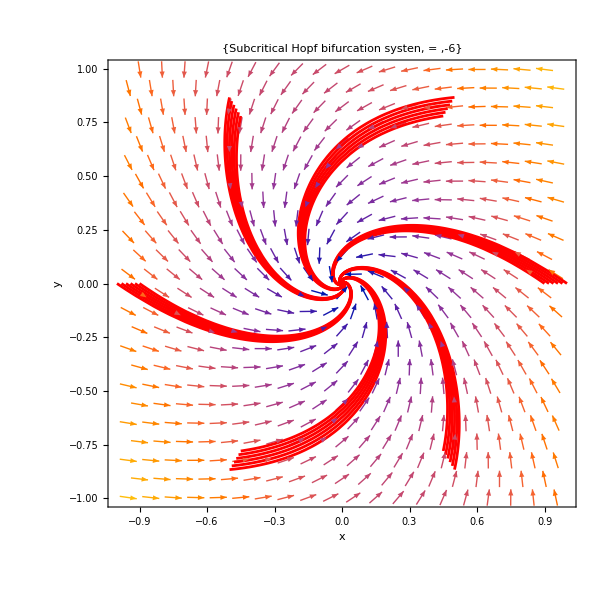

```mathematica
ClearAll["Global`*"]

u = -6;

Equation1 = x'[t] == -5*y[t] + u*x[t] - x[t]^3;
Equation2 = y'[t] == 5*x[t] + u*y[t] + 3*y[t]^3;

System1 = {Equation1, Equation2};

FixPoint1 = {0, 0};

t0 = 0;
tMax = 5;

(* Create 10 circles with different radii on which the initialPoints lie *)
nrOfInitialPoints = 6;
radiusMin = 0.9;
radiusMax = 1.0;

initialPoints = Table[
   {x[0] == FixPoint1[[1]] + radius*Cos[2 Pi k/nrOfInitialPoints], 
    y[0] == FixPoint1[[2]] + radius*Sin[2 Pi k/nrOfInitialPoints]},
   {radius, Range[radiusMin, radiusMax, (radiusMax - radiusMin)/(nrOfInitialPoints - 1)]},
   {k, nrOfInitialPoints}
];

(* Flatten the list to get a single list of initial points *)
initialPoints = Flatten[initialPoints, 1];

(* Use NDSolve for each initial point and store the solutions in a list *)
solutions = Table[NDSolve[{System1, initialPoints[[i]]}, {x, y}, {t, t0, tMax}], {i, Length[initialPoints]}];

(* Plot the trajectories for each solution with arrows indicating the direction *)
TrajectoryPlotArrows = Table[
   ParametricPlot[Evaluate[{x[t], y[t]} /. solution], {t, t0, tMax}, PlotStyle -> Red],
   {solution, solutions}
];

(* Add arrows indicating the direction using VectorPlot *)
VectorPlotArrows = VectorPlot[{-5*y+u*x -x^3,5*x+u*y+3*y^3}, {x, -1, 1}, {y, -1, 1},
   VectorPoints -> 20, VectorScale -> 0.03, VectorStyle -> Directive[Black]];

(* Show the combined plot *)
Show[VectorPlotArrows, TrajectoryPlotArrows, FrameLabel -> {"x", "y"}, 
  PlotLabel -> {"Subcritical Hopf bifurcation systen,  = ", u}, ImageSize -> 600]
```

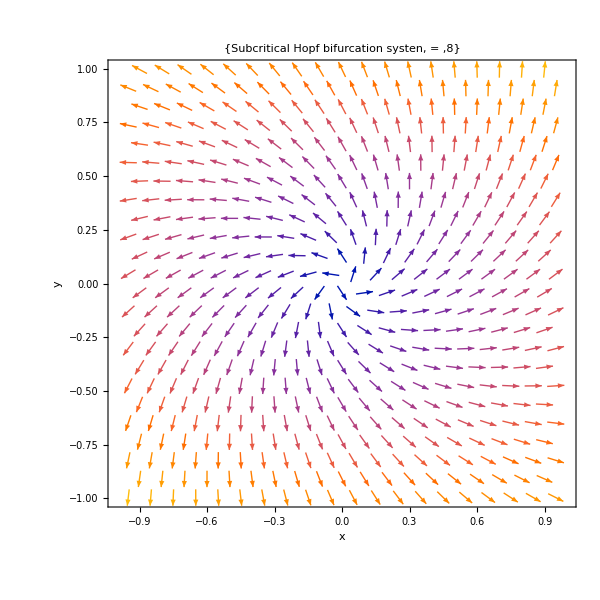

```mathematica
ClearAll["Global`*"]

u = 8;

Equation1 = x'[t] == -5*y[t] + u*x[t] - x[t]^3;
Equation2 = y'[t] == 5*x[t] + u*y[t] + 3*y[t]^3;

System1 = {Equation1, Equation2};

FixPoint1 = {0, 0};

t0 = 0;
tMax = 5;

(* Create 10 circles with different radii on which the initialPoints lie *)
nrOfInitialPoints = 8;
radiusMin = 0.01;
radiusMax = 0.01;

initialPoints = Table[
   {x[0] == FixPoint1[[1]] + radius*Cos[2 Pi k/nrOfInitialPoints], 
    y[0] == FixPoint1[[2]] + radius*Sin[2 Pi k/nrOfInitialPoints]},
   {radius, Range[radiusMin, radiusMax, (radiusMax - radiusMin)/(nrOfInitialPoints - 1)]},
   {k, nrOfInitialPoints}
];

(* Flatten the list to get a single list of initial points *)
initialPoints = Flatten[initialPoints, 1];

(* Use NDSolve for each initial point and store the solutions in a list *)
solutions = Table[NDSolve[{System1, initialPoints[[i]]}, {x, y}, {t, t0, tMax}], {i, Length[initialPoints]}];

(* Plot the trajectories for each solution with arrows indicating the direction *)
TrajectoryPlotArrows = Table[
   ParametricPlot[Evaluate[{x[t], y[t]} /. solution], {t, t0, tMax}, PlotStyle -> Red],
   {solution, solutions}
];

(* Add arrows indicating the direction using VectorPlot *)
VectorPlotArrows = VectorPlot[{-5*y+u*x -x^3,5*x+u*y+3*y^3}, {x, -1, 1}, {y, -1, 1},
   VectorPoints -> 20, VectorScale -> 0.03, VectorStyle -> Directive[Black]];

Show[VectorPlotArrows, TrajectoryPlotArrows, FrameLabel -> {"x", "y"}, 
  PlotLabel -> {"Subcritical Hopf bifurcation systen,  = ", u}, ImageSize -> 600]
```

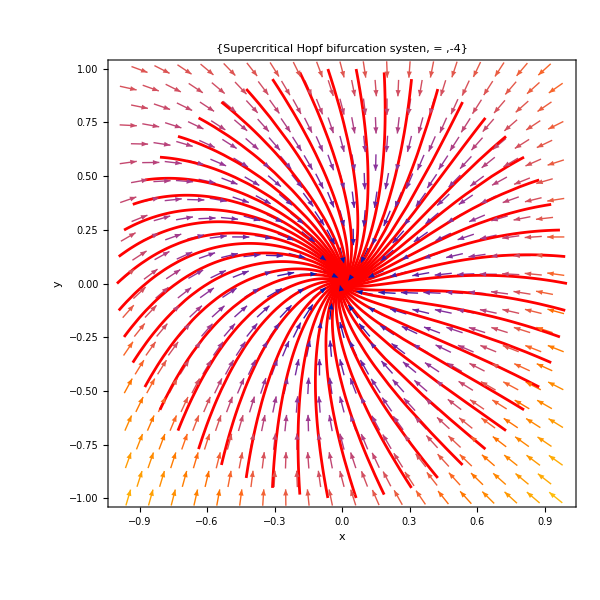

```mathematica
ClearAll["Global`*"]

u = -4;

Equation1 = x'[t] == y[t] + u*x[t] - x[t]^2;
Equation2 = y'[t] == -x[t] + u*y[t] + 2*x[t]^2;

System1 = {Equation1, Equation2};

FixPoint1 = {0, 0};

t0 = 0;
tMax = 5;

(* Create 10 circles with different radii on which the initialPoints lie *)
nrOfInitialPoints = 50;
radiusMin = 1.0;
radiusMax = 1.0;

initialPoints = Table[
   {x[0] == FixPoint1[[1]] + radius*Cos[2 Pi k/nrOfInitialPoints], 
    y[0] == FixPoint1[[2]] + radius*Sin[2 Pi k/nrOfInitialPoints]},
   {radius, Range[radiusMin, radiusMax, (radiusMax - radiusMin)/(nrOfInitialPoints - 1)]},
   {k, nrOfInitialPoints}
];

(* Flatten the list to get a single list of initial points *)
initialPoints = Flatten[initialPoints, 1];

(* Use NDSolve for each initial point and store the solutions in a list *)
solutions = Table[NDSolve[{System1, initialPoints[[i]]}, {x, y}, {t, t0, tMax}], {i, Length[initialPoints]}];

(* Plot the trajectories for each solution with arrows indicating the direction *)
TrajectoryPlotArrows = Table[
   ParametricPlot[Evaluate[{x[t], y[t]} /. solution], {t, t0, tMax}, PlotStyle -> Red],
   {solution, solutions}
];

(* Add arrows indicating the direction using VectorPlot *)
VectorPlotArrows = VectorPlot[{y+u*x -x^2,-x+u*y+2*x^2}, {x, -1, 1}, {y, -1, 1},
   VectorPoints -> 20, VectorScale -> 0.03, VectorStyle -> Directive[Black]];

(* Show the combined plot *)
Show[VectorPlotArrows, TrajectoryPlotArrows, FrameLabel -> {"x", "y"}, 
  PlotLabel -> {"Supercritical Hopf bifurcation systen,  = ", u}, ImageSize -> 600]
```

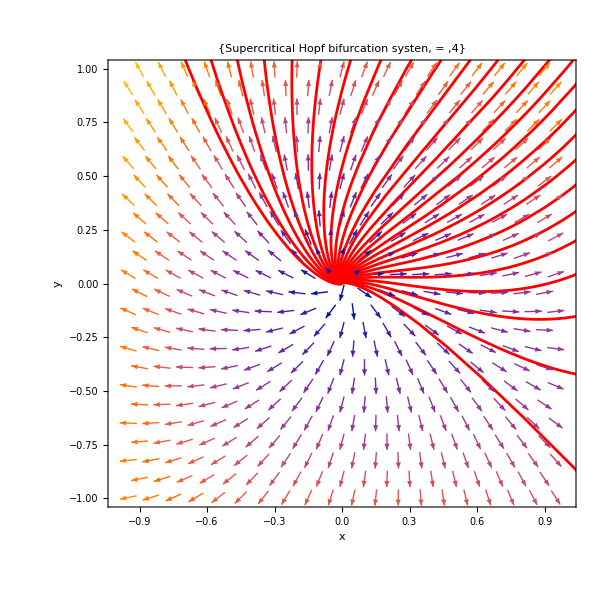

```mathematica
ClearAll["Global`*"]

u = 4;

Equation1 = x'[t] == y[t] + u*x[t] - x[t]^2;
Equation2 = y'[t] == -x[t] + u*y[t] + 2*x[t]^2;

System1 = {Equation1, Equation2};

FixPoint1 = {0, 0};

t0 = 0;
tMax = 5;

(* Create 10 circles with different radii on which the initialPoints lie *)
nrOfInitialPoints = 50;
radiusMin = 0.001;
radiusMax = 0.001;

initialPoints = Table[
   {x[0] == FixPoint1[[1]] + radius*Cos[2 Pi k/nrOfInitialPoints], 
    y[0] == FixPoint1[[2]] + radius*Sin[2 Pi k/nrOfInitialPoints]},
   {radius, Range[radiusMin, radiusMax, (radiusMax - radiusMin)/(nrOfInitialPoints - 1)]},
   {k, nrOfInitialPoints}
];

(* Flatten the list to get a single list of initial points *)
initialPoints = Flatten[initialPoints, 1];

(* Use NDSolve for each initial point and store the solutions in a list *)
solutions = Table[NDSolve[{System1, initialPoints[[i]]}, {x, y}, {t, t0, tMax}], {i, Length[initialPoints]}];

(* Plot the trajectories for each solution with arrows indicating the direction *)
TrajectoryPlotArrows = Table[
   ParametricPlot[Evaluate[{x[t], y[t]} /. solution], {t, t0, tMax}, PlotStyle -> Red],
   {solution, solutions}
];

(* Add arrows indicating the direction using VectorPlot *)
VectorPlotArrows = VectorPlot[{y+u*x -x^2,-x+u*y+2*x^2}, {x, -1, 1}, {y, -1, 1},
   VectorPoints -> 20, VectorScale -> 0.03, VectorStyle -> Directive[Black]];

Show[VectorPlotArrows, TrajectoryPlotArrows, FrameLabel -> {"x", "y"}, 
  PlotLabel -> {"Supercritical Hopf bifurcation systen,  = ", u}, ImageSize -> 600]
```